# Epispiral

### 参考

### https://mathworld.wolfram.com/Epispiral.html

The epispiral is a plane curve with polar equation
r = a sec(n θ) . 
There are n sections if n is odd and 2 n if n is even .

```mathematica
Manipulate[PolarPlot[a Sec[n θ],{θ,0,2π},Exclusions->"Singularities",PlotRange->4],{a,1,3},{n,2,9,1}]
```

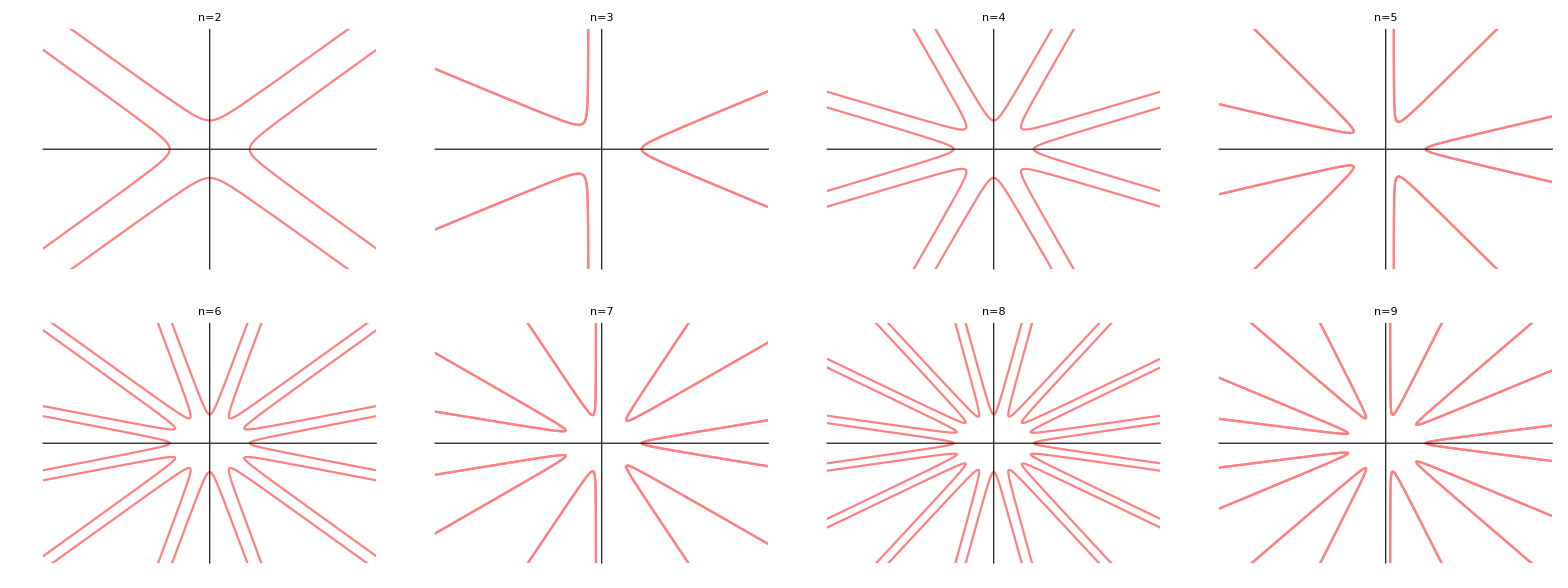

```mathematica
Partition[Table[PolarPlot[Sec[n θ],{θ,0,2π},Exclusions->"Singularities",PlotLabel->StringForm["n=``",n],PlotRange->4,PlotStyle->Pink,Ticks->None],{n,2,9}],4]//Grid
```

```mathematica
A slightly more symmetric version considers instead
r=a|sec(n θ)|
```

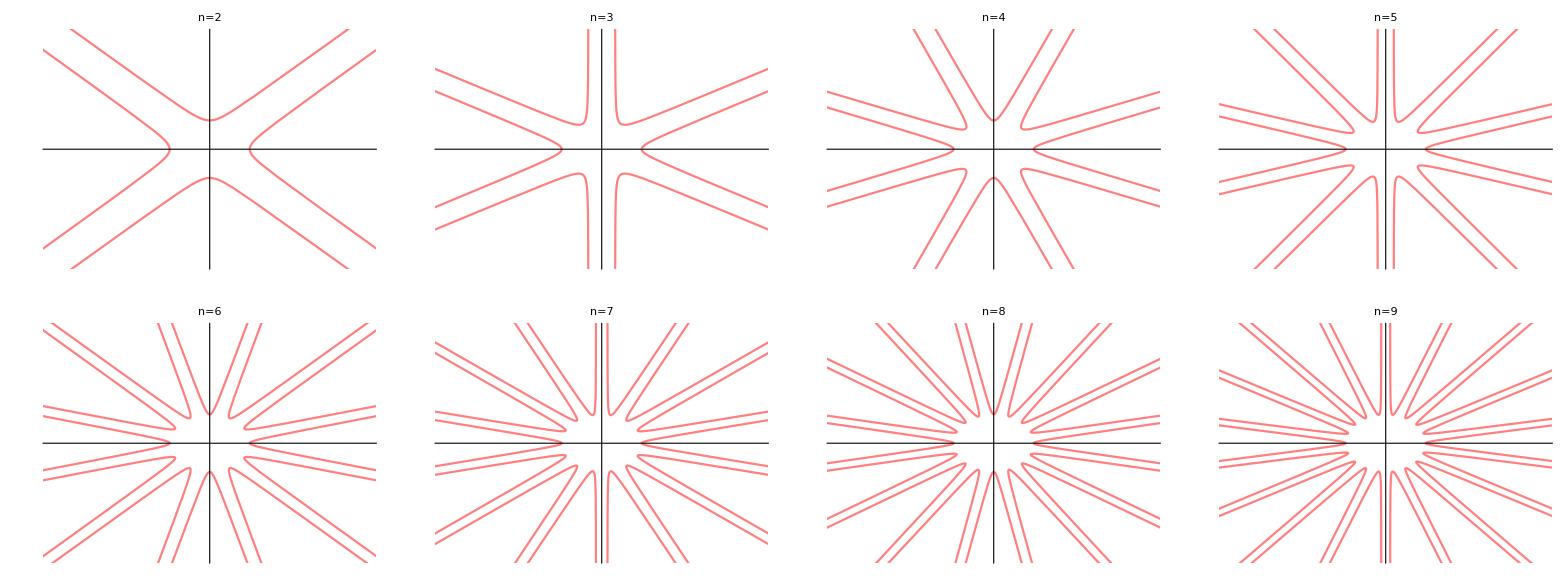

```mathematica
Partition[Table[PolarPlot[Abs@Sec[n θ],{θ,0,2π},Exclusions->"Singularities",PlotLabel->StringForm["n=``",n],PlotRange->4,PlotStyle->Pink,Ticks->None],{n,2,9}],4]//Grid
```